# NSB Entropy Estimation Christian B. Mendl, (c) 2009 - 2011

### References

Ilya Nemenman, Fariel Shafee, and William Bialek. Entropy and Inference, Revisited. In T. G. Dietterich, S. Becker, and Z. Ghahramani, editors, Advances in Neural Information Processing Systems 14, Cambridge, MA (2002). MIT Press. [http://arxiv.org/abs/physics/0108025]; C++ and Matlab implementation by Ilya Nemenman is available at [http://nsb-entropy.sourceforge.net]
Ilya Nemenman. Inference of entropies of discrete random variables with unknown cardinalities. (2002) [http://arxiv.org/abs/physics/0207009]
Ilya Nemenman, William Bialek, and Rob de Ruyter van Steveninck. Entropy and information in neural spike trains: Progress on the sampling problem. Physical Review E 69, 056111 (2004)

### Load computation routines

```mathematica
SetDirectory[NotebookDirectory[]];
<<nsb_entropy_base.m;
```

### Values from the Readme file of the original Matlab Implementation

```mathematica
counts=Rationalize[Import["pooled/0.300.mat"]];
counts=counts//.{x_List}:>x;
(*counts=RandomInteger[{1,9},2183721];*)
EntropyNSB[counts]
```

NIntegrate::precw: The precision of the argument function ((2 ⅇ^(1.74884×10^7-514 LogGamma[(«1»)/(«1»)]+«47»+«1»+«187») ω («99»+«183») (-PolyGamma[1,1+ω^2/Plus[«2»]^2]+514 PolyGamma[1,1+(514 ω^2)/Plus[«2»]^2]))/(1-ω)^3) is less than WorkingPrecision (60.).

NIntegrate::precw: The precision of the argument function ((2 ⅇ^(1.74884×10^7-514 LogGamma[(«1»)/(«1»)]+«47»+«1»+«187») ω (-PolyGamma[1,1+ω^2/Plus[«2»]^2]+514 PolyGamma[1,1+(514 ω^2)/Plus[«2»]^2]))/(1-ω)^3) is less than WorkingPrecision (60.).

4.0683933665803856447271807202430702679097373092622945113781

### Show the effect of the substitution β→(ω/(1-ω))^2

```mathematica
Subscript[nx, T]=Union[Subscript[n, T]]
Subscript[kx, T]=Count[Subscript[n, T],#]&/@Subscript[nx, T]
Subscript[M, T]=Total[Subscript[n, T]]
Subscript[K, T]=Total[Subscript[kx, T]]
Subscript[K1, T]=Subscript[K, T]-First[Subscript[kx, T]]
Subscript[L0, T]=ρLog[κ/Subscript[K, T]/.FindRoot[Subscript[K1, T]/κ+PolyGamma[κ]-PolyGamma[Subscript[M, T]+κ],{κ,1}],Subscript[nx, T],Subscript[kx, T]];
```

{0,2,3,4}

{3,3,1,2}

17

9

6

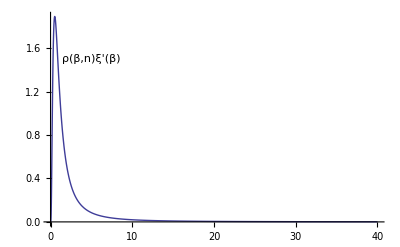

```mathematica
Show[{Plot[ρ[β,Subscript[nx, T],Subscript[kx, T],Subscript[L0, T]] dξ[β,Length[Subscript[n, T]]],{β,0,40},PlotRange->All,AxesLabel->{β}],Graphics[Text["ρ(β,n)ξ'(β)",{5,1.5}]]}]
```

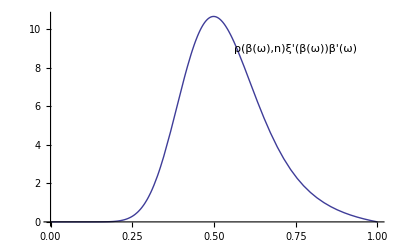

```mathematica
Show[{Plot[ρ[β,Subscript[nx, T],Subscript[kx, T],Subscript[L0, T]] dξ[β,Length[Subscript[n, T]]](2ω)/(1-ω)^3/.β->(ω/(1-ω))^2,{ω,0,1},AxesLabel->{ω}],Graphics[Text["ρ(β(ω),n)ξ'(β(ω))β'(ω)",{0.75,9}]]}]
```

### Reproduce figure 4 (a) for β==1 in "Entropy and Inference, Revisited"

```mathematica
Pdirichlet[β_,K_]:=Module[{q=ConstantArray[0,K]},For[i=1,i<K,i++,q⟦i⟧=(1-Total[q⟦1;;i-1⟧])RandomReal[BetaDistribution[β,(K-i)β](*,WorkingPrecision->40*)]];q⟦K⟧=1-Total[q⟦1;;K-1⟧];q]
```

```mathematica
EntropyProb[q_]:=-Total[If[#==0,0,#Log[#]]&/@q]
```

9.34854

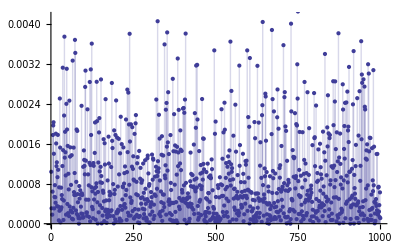

```mathematica
Subscript[q, T]=Pdirichlet[(*2/100*)1,1000];
EntropyProb[Subscript[q, T]]/Log[2]
ListPlot[Subscript[q, T],Filling->Axis]
```

```mathematica
(* simulate M experimental random counts based on the probability distribution q *)
RandomCount[q_,M_]:=BinCounts[RandomReal[{0,1},M],{Prepend[Accumulate[q],0]}]
```

```mathematica
Needs["ErrorBarPlots`"];
```

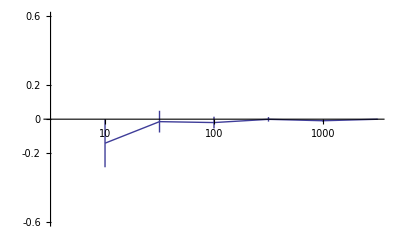

```mathematica
Subscript[s, T]=EntropyProb[Subscript[q, T]];
Subscript[M, T]={10,30,100,300,1000,3000};
ErrorListPlot[{(EntropyNSB[#]-Subscript[s, T])/Subscript[s, T],DeltaEntropyNSB[#]/Subscript[s, T]}&/@(RandomCount[Subscript[q, T],#]&/@Subscript[M, T]),Joined->True,AxesOrigin->{0,0},PlotRange->{{0,Length[Subscript[M, T]]},{-0.6,0.6}},Ticks->{{#,Subscript[M, T]⟦#⟧}&/@Range[Length[Subscript[M, T]]],{-0.6,-0.2,0,0.2,0.6}}]
```